```mathematica
a=Import["C:\\Users\\Расим\\Desktop\\2019_04_19_22_18_57-NRP15-e1-UDAR.txt","Table"];
```

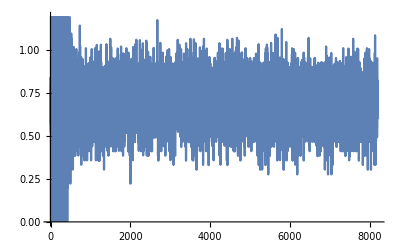

```mathematica
ListLinePlot[a[[All,4]]]
```

C:\Users\Расим\Desktop\File1.txt

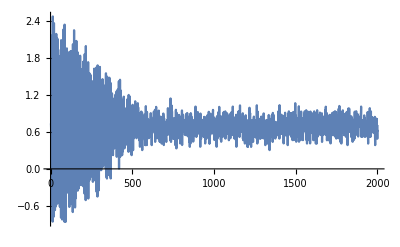

```mathematica
a1=Table[a[[n,4]],{n,1,2000}];
Export["C:\\Users\\Расим\\Desktop\\File1.txt",a1]
ListLinePlot[a1, PlotRange->All]
```

```mathematica
model=e*Exp[-x^2/(2b^2)]*Exp[-c^2*(1-Cos[d*x])];
File3=Import["C:\\Users\\Расим\\Desktop\\File3.txt","List"];
F3=ToExpression[File3];
File4=Import["C:\\Users\\Расим\\Desktop\\File4.txt","List"];
F4=ToExpression[File4];
data=Table[{F4[[n]],F3[[n]]},{n,1,Length[File3]}];
fit=FindFit[a1,model,{e,b,c,d},x]
modelf=Function[{x},Evaluate[model/.fit]];
Plot[modelf[x],{x,0,1000}];
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{e→0.700895,b→6753.,c→-0.000107859,d→16.1009}

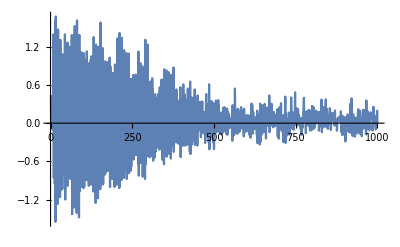

```mathematica
a2=Import["C:\\Users\\Расим\\Desktop\\2019_04_19_22_18_57-SRP3-e1-UDAR.txt","Table"];

For[n=1,n<8191,n=n+32,a3=Table[a2[[n,4]],n]];
a3=Table[a2[[n,4]],{n,1,8191,32}];
a4=Table[a2[[n,4]],{n,1,1000}];
ListLinePlot[a4]
```

```mathematica
(*li={{12,2.176},{14,2.478},{16,1.735},{19,1.742},{21,2.369},{28,1.895},{35,2.194},{42,2.116},{44,1.86},{49,1.732},{56,1.751},{58,1.835},{63,1.939},{65,2.093},{70,2.018},{72,2.067},{77,1.88},{79,2.266},{84,1.978},{86,2.345},{91,1.924},{93,1.939},{100,1.959},{114,1.899},{123,1.915},{130,1.913},{135,1.821},{137,2.026},{142,1.826},{144,2.254},{151,2.062},{158,2.08},{165,1.899},{172,1.766},{181,1.84},{200,1.742}};
model2=y*Exp[-t^2/(2u^2)]*Exp[-i^2*(1-Cos[o*t])];
fits=FindFit[li,model2,{y,u,i,o},t];*)
```

```mathematica
data2=Table[a[[n,4]],{n,1,1000}];
model2=u*Exp[-x^2/(2j^2)]*Exp[-o^2*(1-Cos[p*x])]
fit2=FindFit[data2,model2,{u,j,o,p},x]
```

ⅇ^(-x^2/(2 j^2)-o^2 (1-Cos[p x])) u

{u→0.706637,j→3465.73,o→-0.0896036,p→16.1865}

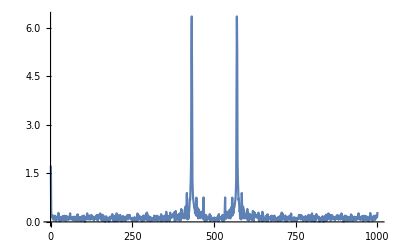

C:\Users\Расим\Desktop\fur1.txt

```mathematica
four=Abs[Fourier[a4]];
ListLinePlot[four, PlotRange->All]
Export["C:\\Users\\Расим\\Desktop\\fur1.txt",four]
Max[four];
For[i=0,i<1000,i++,If[four[[i]]>0.35,Position[four[[i]]]]];
```

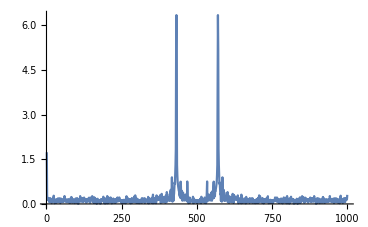
```mathematica
(-Graphics-_□)_(□_□)
```

```mathematica
((-Graphics-_□)_(□_□))_(□_□)
```

{{26,1.76933},{28,2.28078},{60,1.04358},{63,1.85045},{84,1.86628},{86,2.26964},{109,1.53882},{125,0.99927},{128,1.78269},{144,2.02614},{172,1.65663},{190,1.0076},{230,1.73218},{232,1.43424}}

{1.76933,2.28078,1.04358,1.85045,1.86628,2.26964,1.53882,0.99927,1.78269,2.02614,1.65663,1.0076,1.73218,1.43424}

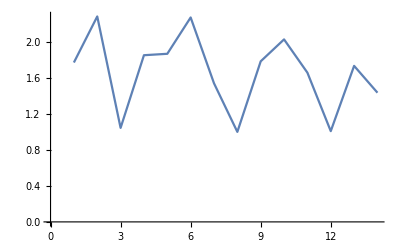

Divide::infy: Infinite expression (3.06845×10^-118)/0. encountered.

{e1→1.,b1→1.,c1→1.,d1→1.}

```mathematica
filter=Import["C:\\Users\\Расим\\Desktop\\Filter.txt","Table"];
filter1=Table[filter[[n,2]],{n,1,250}];
Peaks=FindPeaks[filter1];
Peaks[[All,2]];
Peaks1=FindPeaks[filter1,5]
Peaks1[[All,2]]
ListLinePlot[Peaks1[[All,2]]]
model4=e1*Exp[-x^2/(2b1^2)]*Exp[-c1^2*(1-Cos[d1*x])];
f1=FindFit[Peaks1,model4,{e1,b1,c1,d1},x]
modelf=Function[{x},Evaluate[model4/.f1]];
Plot[modelf[x],{x,0,250}];
```

```mathematica
NonlinearModelFit[Peaks1,e2*Exp[-c2^2*(1-Cos[d2*x])],{e2,c2,d2},x]
```

FittedModel[166126. ⅇ^(-2.23049×10^-15 (1-Cos[1. x]))]